```mathematica
cells = {Photo,Digest,Sting,Vascular,Fat,Sense,Egg,Muscle};
particles = {Cell,Energy,Pellet,Buffer};
```

```mathematica
AnalyzeFrame[frameNo_]:=Module[{path,i,items,ptct},
Quiet[
path = StringForm["D:\\better output 2\\output\\frame``.json",frameNo];
{i}=Import[path//ToString];
items = "Items"/.i;
ptct= {"pt","ct"}/.items;
{
Table[Count[ptct,{i,_}],{i,0,4}],
Table[Count[ptct,{0,i}],{i,0,Length[cells]}]
}
]
]
```

```mathematica
step = 408000;
skipSize=Floor[step/50]
```

8160

```mathematica
PlotTimeEvolution[fMax_]:=Module[{data},
ProgressIndicator[Dynamic[n],{0,fMax}]//PrintTemporary;
data =Table[n=i;AnalyzeFrame[i],{i,0,fMax,skipSize}]//Transpose;
{data//Last//Transpose,data//First//Transpose}
]
```

```mathematica
skipSize = 10000;
```

```mathematica
{data1,data2}=PlotTimeEvolution[step];
```

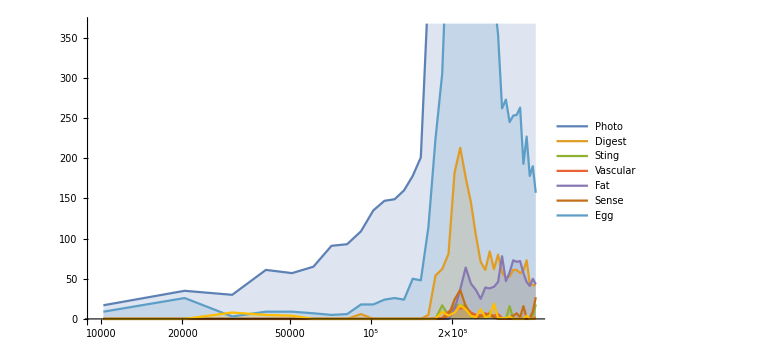

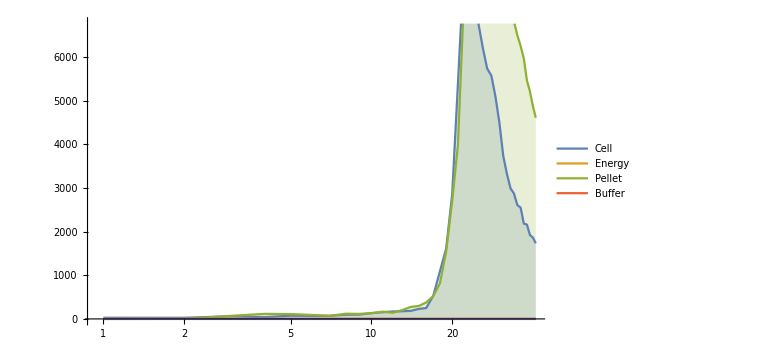

```mathematica
ListLogLinearPlot[data1,PlotLegends->cells,Joined->True,ImageSize->Large,Filling->Bottom,DataRange->{0,step}]
ListLogLinearPlot[data2,PlotLegends->particles,Joined->True,ImageSize->Large,Filling->Bottom]
```

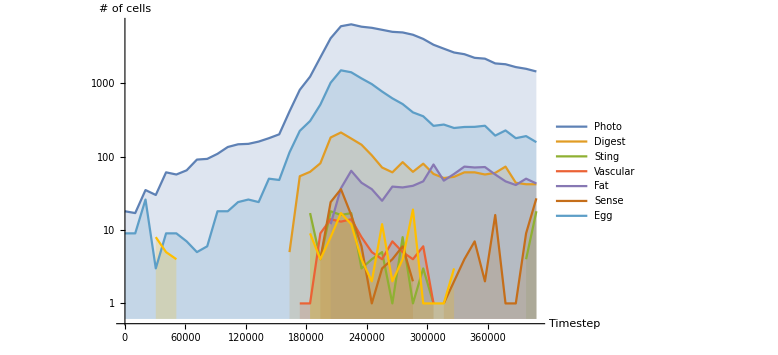

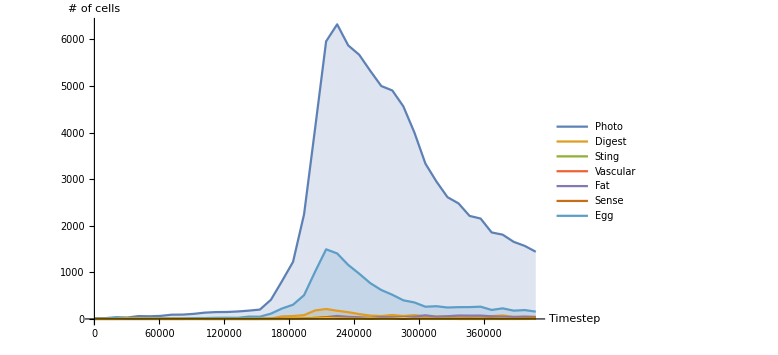

```mathematica
ListLogPlot[data1,PlotLegends->cells,Joined->True,ImageSize->Large,Filling->Bottom,DataRange->{0,step},AxesLabel->{"Timestep","# of cells"}]
plot=ListPlot[data1,PlotLegends->cells,Joined->True,ImageSize->Large,Filling->Bottom,DataRange->{0,step},AxesLabel->{"Timestep","# of cells"},PlotRange->All]
```